# What playable characters should there be in a future Shovel Knight game?

## by fpdotmonkey

## tl;dr

Shovel Knight, Bard, and two of (Black Knight, Shield Knight, Tinker Knight, Propellor Knight, Reize, Polar Knight, Mr Hat) because they are representative of the kinds of characters people voted for.

## Introduction

Shovel Knight: Treasure Trove is a platforming game created by Yacht Club Games with a series of campaigns where, playing as different characters in each, you fight the evil Order of No Quarter while meeting friends and battling travelers along the way.  The first of these campaigns featured the titular Shovel Knight, and subsequent campaigns, as voted by the game’s large and active community, feature Plague Knight, Specter Knight, and King Knight, with the ladder campaign yet to be released.

It’s been a while since Yacht Club polled which would be the playable DLC characters (with information about it here), and members of the community often lament that their favorite character wasn’t selected.  So if Yacht Club were to announce a new Treasure Trove-style game today where there are four campaigns with a different playable character in each, what characters would the community prefer?

To answer this question, I created a poll on 12 April 2018 asking members of the community “Who should get the next Shovel Knight Campaign?” with these options, each person voting for four knights.  The portraits below were made by Yacht Club with the exception of the Troupple King, which I made.  They can all be found HERE.

```mathematica
knights={"Bard","Baz","Black Knight","King Knight","Mole Knight","Mr Hat","Phantom Striker","Plague Knight","Polar Knight","Propellor Knight","Reize","Shield Knight","Shovel Knight","Specter Knight","Tinker Knight","Treasure Knight","Troupple King"};
portraits=ImageCrop[#,{128,128}]&/@(Import/@FileNames["*.png",NotebookDirectory[]<>"SK_portraits"]);
Column/@Thread[{knights,portraits}]
```

{Bard
-Graphics-,Baz
-Graphics-,Black Knight
-Graphics-,King Knight
-Graphics-,Mole Knight
-Graphics-,Mr Hat
-Graphics-,Phantom Striker
-Graphics-,Plague Knight
-Graphics-,Polar Knight
-Graphics-,Propellor Knight
-Graphics-,Reize
-Graphics-,Shield Knight
-Graphics-,Shovel Knight
-Graphics-,Specter Knight
-Graphics-,Tinker Knight
-Graphics-,Treasure Knight
-Graphics-,Troupple King
-Graphics-}

The analysis I’m doing was done with Mathematica.  If you’d like to play with this stuff yourself, you can download the Wolfram Engine, which is free and play with my code.  You don’t need to read the codee to understand what’s going on though, but it may enhance your experience if you do.

Why these knights?  They are the playable characters from Treasure Trove, the knights who you do battle with, and other characters important to the story.  Notably this list leaves out The Enchantress compared to the poll done by Yacht Club for Treasure Trove, and adds in The Bard and Troupple King (long may his stem grow!), who are non-combative characters, at least in the campaigns released as of 17 August 2019.  The Enchantress was omitted because at the time of creating the poll, I didn’t know that she was an option in Yacht Club’s poll.  Bard was added because I thought he was an interesting character, and the Troupple King was added due to his immense might and majesty and also kind of as a joke.

## Data Analysis

### Import and Prepare Data

The survey data can be found HERE.  To start, I’ll format the data in a consistent way that’ll be useful for later.

```mathematica
surveyData=Import[NotebookDirectory[]<>"Who should get the next Shovel Knight Campaign? (Responses) - Cleaned up data.csv","CSV"];
surveyData⟦1⟧=Nothing; (*Remove the column headers*)
(*Remove extreanneous bits from the character names used in the survey*)
surveyData=Map[StringReplace[#," (again)"->""]&,surveyData,{2}];
surveyData=Map[StringReplace[#,"The "->""]&,surveyData,{2}];
surveyData=Map[StringReplace[#,"."->""]&,surveyData,{2}];
```

### What Proportion of Ballots Voted for each Character?

The most obvious way to decide which characters should be selected is to look at which characters got the most votes.

The first thing I’ll do is to create a nice way of plotting the results of this ranking.  Each knight’s name will be plotted at a height related to to the proportion of votes they got, with there vote share next to their name

```mathematica
rankingsPlot[data_,names_]:=Graphics[{{Text[#⟦1⟧,{0,#⟦2⟧},{1,0}]},{Text[#⟦2⟧,{0,#⟦2⟧},{-1.5,0}]}}&/@Thread[{names,data}],AspectRatio->2];
```

To calculate the portion of votes each knight received, I count how many times a knight is voted for and divide that by the number of ballots cast.  The sum of all these vote shares is 4.00 because each person cast 4 votes.  I had to move Black Knight’s name because it was colliding with Shield Knight’s, but they are tied.

```mathematica
ballotPercents=N[Lookup[Counts[Flatten@surveyData⟦All,2;;⟧],#]&/@knights/Length[surveyData],3];
"The sum of vote shares: "<>ToString[Total@ballotPercents]
rankingsPlot[ballotPercents,knights]
```

The sum of vote shares: 4.00

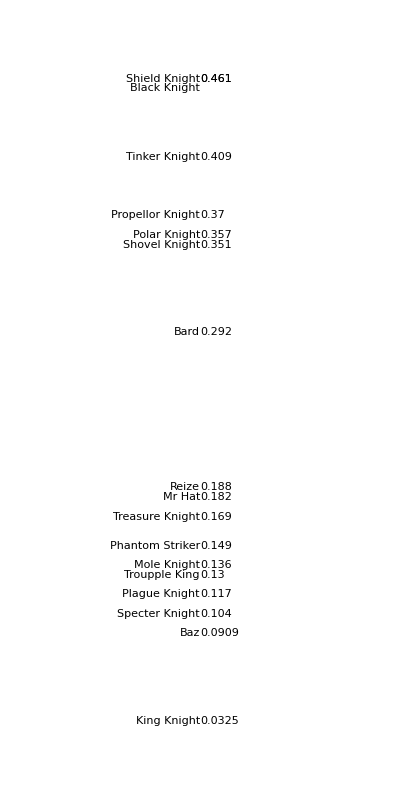

This already presents some interesting results!  It appears that there’s a distribution of highly-voted knights and another of low-voted knights.  Perhaps Yacht Club could select among these highly-voted knights to be featured in their own campaigns.

Outside of these distributions are Bard, who is between them, and King Knight, who is well below.  Bard seems higher than expected, maybe because a lot of world building in Shovel of Hope was done through the stories he tells after receiving music sheets from the player.  King Knight might be low because of anticipation for King of Cards.

The problem with selecting which knights should have a new campaign by directly counting votes is that it assumes the 4 characters people vote for are selected independently, which considering many characters have related narrative or gameplay function, may not be the case.  Perhaps a more representative ranking can be found from considering characters that were often voted together on a ballot.

### Which Pairs of Characters Were Frequently Voted Together?

Perhaps Yacht Club could consider types of characters to include in a future campaign.  Maybe the community were split between several similar characters, Yacht Club could notice and choose one character to represent them.  So here, I’ll attempt to find out what those groups are by looking at which pairs of characters frequently showed up on ballots.

First I’ll create a list of all possible character pairs.  This also includes pairs that are the same but reversed, like (Bard, Mr Hat) and (Mr Hat, Bard), although the count of these reversed pairs will always be the same.

```mathematica
characterPairs=Array[{knights⟦#1⟧,knights⟦#2⟧}&,Length[knights]{1,1}];
```

Next I’ll make a function that scores how strongly each pair was desired.  I’ll do this by calculating the number of ballots that voted for both characters in the pair.  It’s expected that characters would randomly get voted together, so to account for that, I’ll divide the proportion of ballot that voted for a pair by the random chance that that pair would get voted together.  This means that a character that people really like will have a score of a really big number, but a character that people aren’t so hot for will get a score near 0.

```mathematica
votedTogether[data_List,pair_List]:=If[pair⟦1⟧≠pair⟦2⟧,Length[Select[data,MemberQ[#,pair⟦1⟧]&&MemberQ[#,pair⟦2⟧]&]]/Length[data]/((Lookup[#,pair⟦1⟧]Lookup[#,pair⟦2⟧]&@Counts[Flatten@data])/Length[data]^2),0];
```

Now I can calculate the score for each pair by applying votedTogether[] to every character pair.

```mathematica
votedTogetherArray=SparseArray[Apply[Rule,#]&/@Flatten[Thread/@Thread[{characterPairs,Map[votedTogether[surveyData⟦All,2;;⟧,#]&,characterPairs,{2}]}]/.Thread[knights->Range[Length[knights]]],1]];
```

To visualize the character pairs, I’ve made a graphic that shows how often characters were voted together with color, where a dark square corresponds with a greater frequency.

```mathematica
characterPairColorGradient="PigeonTones";
Graphics[{{Tooltip[Inset[portraits⟦#⟧,{#-1,Length[knights]+1},{Left,Top},1],knights⟦#⟧]},{Tooltip[Inset[portraits⟦#⟧,{-1,-#+Length[knights]+1},{Left,Top},1],knights⟦#⟧]}}]&/@Range[Length[knights]];
Show[MatrixPlot[-Log/@Normal[votedTogetherArray]/.∞->None,Frame->False,ImageSize->Full,ColorFunction->characterPairColorGradient],%]
```

-Graphics-

What I notice that’s interesting is that it seems like there’s especially strong connections between Shovel, Plague, Specter, and King Knights.  That’s awfully interesting, as it suggests there might be some sort of vote splitting that may be going on.  To investigate this further, I’ll plot the characters spatially, so characters from pairs that were often voted together are plotted near to each other.  I’ll also draw lines connecting characters with the color of the lines also indicated how often they were voted together.

```mathematica
weightedAdjacencyMatrix=N[Normal[votedTogetherArray]/.{0->∞}];
g=WeightedAdjacencyGraph[weightedAdjacencyMatrix,GraphLayout->"SpectralEmbedding"];

edgeRenderingFunction=({ColorData[characterPairColorGradient][Rescale[-Log[votedTogetherArray⟦Sequence@@#2⟧],MinMax[-(Log/@votedTogetherArray)]]],Line[#1]}&);
vertexRenderingFunction={Tooltip[Inset[portraits⟦#2⟧,#1,{Center,Center},0.1],knights⟦#2⟧]}&;
GraphPlot[g,EdgeShapeFunction->edgeRenderingFunction,VertexShapeFunction->vertexRenderingFunction,ImageSize->Full]
```

-Graphics-

The triangular shape of the graph to me suggests there would be three groups that people ended up voting for.  The playable characters from Shovel of Hope are again evident in this graphic and there appears to be a division between the remaining knights (Mole, Treasure, Tinker, Propellor, Polar, Shield, and Black Knights) and the “secondary” characters (Baz, Phantom Striker, Rieze, Mr Hate, Bard, and Troupple King).

Although intuition is good for finding groups, it’d be nice to have something more formal to back up the existence of these groups.  Mathematica has a function FindGraphCommunities[] which will identify groups that have strong connections within the group relative to the connections that go out of the group.

```mathematica
communities=FindGraphCommunities[g];
Row[Column/@(%/.Thread[Range[Length[knights]]->knights]),"     "]
```

Black Knight
Mole Knight
Polar Knight
Propellor Knight
Shield Knight
Tinker Knight
Treasure KnightBard
Baz
Mr Hat
Phantom Striker
Reize
Troupple KingKing Knight
Plague Knight
Shovel Knight
Specter Knight

This is very good; it confirms the suspicion that on the whole, the people that voted tended to vote for groups of characters.  But this doesn’t immediately say which characters should be selected.  I’ll look at this in the next section.

### Which characters should be selected?

Our goal here will be to make a ranking of which characters are favorable, just like I did when I counted up the totals initially.  But now each character will be ranked not only on how many votes they got, but also on how many votes they got relative to the rest of their character group that was found in the previous section.

First I’ll calculate the average number of votes each group got from a ballot.

```mathematica
communityStrengths=Thread[{communities/.Thread[Range[Length[knights]]->knights],Total/@(Map[Tally,Array[MemberQ@@{communities⟦#1⟧/.Thread[Range[Length[knights]]->knights],surveyData⟦#2,#3+1⟧}&,{Length[communities],Length[surveyData],Length[surveyData⟦1⟧]-1}],{2}]/.{False,_}->Nothing/.{}->Nothing/.{{True,x_}}->x)/Length[surveyData]}];

Transpose@%//N//TableForm
```

Black Knight
Mole Knight
Polar Knight
Propellor Knight
Shield Knight
Tinker Knight
Treasure Knight | Bard
Baz
Mr Hat
Phantom Striker
Reize
Troupple King | King Knight
Plague Knight
Shovel Knight
Specter Knight
2.36364 | 1.03247 | 0.603896

So the average ballot gave the knights about 21/3 votes, 1 vote for the secondary characters, and about 2/3 of a vote for the already-playable characters.

But it’s natural that the knights would get the most votes, since they are the biggest group.  So I should find out how many votes each group got per character.

```mathematica
averageVotePerCharacterGivenCommunity=Thread[{communities,Table[#⟦i,2⟧/Length[#⟦i,1⟧]&[communityStrengths],{i,Length[communityStrengths]}]//N}];

Transpose@(%/.Thread[Range[Length[knights]]->knights])//TableForm
```

Black Knight
Mole Knight
Polar Knight
Propellor Knight
Shield Knight
Tinker Knight
Treasure Knight | Bard
Baz
Mr Hat
Phantom Striker
Reize
Troupple King | King Knight
Plague Knight
Shovel Knight
Specter Knight
0.337662 | 0.172078 | 0.150974

So each knight got about 1/3 of a vote on the average ballot, secondary characters got about 1/6, and already-playable characters also got about 1/7.

Finally, I’ll take the actual portion of the vote each knight got and divide that by this expected portion of the vote to get a score that I can make a ranking out of.

```mathematica
knightPreferenceNormalizedByCommunity=ballotPercents/Sort[Flatten[Thread/@averageVotePerCharacterGivenCommunity,1],#2⟦1⟧>#1⟦1⟧&]⟦All,2⟧;

Show[rankingsPlot[knightPreferenceNormalizedByCommunity,knights],ImageSize->Full]
```

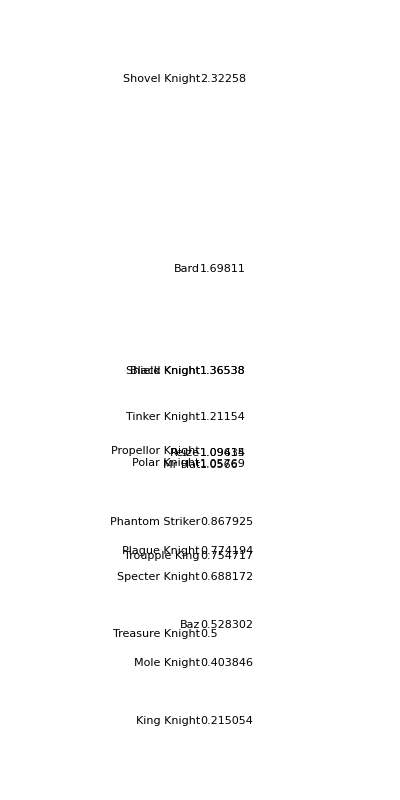

Any character in this scoring with a score of more than 1.0 is wanted more than average compared to their character group.  So by an overwhelming margin, Shovel Knight is the winner by this ranking, with Bard making a come-from-behind runner-up.

## Results

So based on these scores, I’d say that the community definitely would like to see Shovel Knight come back as a playable character.  Bard is probably someone the community would like to see as well, although I suspect that some of hit votes might have come from people reacting to the novelty of the idea of him being included.  The community would also like to see any of Shield Knight, Black Knight, Tinker Knight, Propeller Knight, Reize, Polar Knight, or Mr Hat, although none of these characters commanded such a high score to suggest that the community demands any of them specifically like Shovel Knight or Bard.

So does this roster accurately reflect the desires of the community?  It’s more representative than just looking at the 4 characters with the most votes, but probably not perfect.

The most serious issue is that the poll was taken before the release date of King of Cards.  King Knight' s vote share likely suffered because a game featuring him is coming soon.  The other characters may also show performances in that game that will change their opinion within the Shovel Knight community.  Bard is meant to be prominently featured, so perhaps his vote share could go even higher.

Thank you so much for reading to the end.  This ended up being kind of long, and it took me waaay longer than I expected, so I really appreciate that you took the time to read what I had to say.